```mathematica
<<"C:\\Users\\aliha\\Desktop\\Lineage-Mapper\\LineageMapperTools\\lineagemapperTools.m";
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\Lineage-Mapper\\edge tracking\\edgetrack.m";
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\Lineage-Mapper\\vertex tracking\\vertextrack.m";
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\Lineage-Mapper\\Lineage-Mapper\\lineagemapper.m";
```

```mathematica
dir = "C:\\Users\\aliha\\Desktop\\scripts-codes\\github codes\\lineage mapper\\Segmentation_Movies\\movies 2";
SetDirectory[dir]; 
filesNames=FileNames["*.tiff"];
```

```mathematica
ordering=Ordering@Flatten@StringCases[filesNames,x:DigitCharacter..~~__:> ToExpression@x];
```

```mathematica
filesNames=filesNames[[ordering]];
```

```mathematica
ListAnimate[Import[dir<>"\\"<>#]&/@filesNames]
```

```mathematica
segs = segmentImage@Import[dir<>"\\"<>#]&/@filesNames;
```

```mathematica
({segmentedstacks,links}=cellTracker[segs,"segmented"-> True];)//AbsoluteTiming
```

{10.8262,Null}

```mathematica
ListAnimate[Map[Colorize]@segmentedstacks]
```

```mathematica
neighboursQuery[segmentedstacks[[1]]] (* cell neighbours in a particular frame *)
```

Dataset[<>]

```mathematica
Rasterize[Graphics@centroidMap[segmentedstacks],"Image",ImageSize->Large]
```

-Graphics-

```mathematica
cellTrackMov[segmentedstacks,2,"cropped"->True,"duration"->2]
```

```mathematica
cellTrackMov[segmentedstacks,{2,15},"duration"-> 2]
```

```mathematica
dir = "C:\\Users\\aliha\\Desktop\\scripts-codes\\github codes\\lineage mapper\\Segmentation_Movies\\movies 1";
SetDirectory[dir]; 
filesNames=FileNames["*.tiff"];
```

```mathematica
ordering=Ordering@Flatten@StringCases[filesNames,x:DigitCharacter..~~__:> ToExpression@x];
```

```mathematica
filesNames=filesNames[[ordering]];
```

```mathematica
segs = segmentImage@Import[dir<>"\\"<>#]&/@filesNames;
```

```mathematica
ListAnimate[Import[dir<>"\\"<>#]&/@filesNames]
```

```mathematica
$framehistory={};
({segmentedstacks,links}=Quiet@cellTracker[segs,"segmented"->True];)//AbsoluteTiming
```

{14.5421,Null}

```mathematica
ListAnimate[Map[Colorize]@segmentedstacks]
```

```mathematica
edgeAssociation[segmentedstacks,images];
```

```mathematica
trackedEdgeMask[segmentedstacks,1,4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimate[plotEdge[segmentedstacks,images,1,4]]
```

## Test 2

```mathematica
(* lineage tree and table *)
```

```mathematica
dir = "C:\\Users\\aliha\\Desktop\\scripts-codes\\miscellaneous wolfram codes\\edge detect\\steven -ali - mesh\\test";
SetDirectory[dir]; 
filesNames=FileNames["*.tiff"];
```

```mathematica
lineagemappersegs=Import["C:\\Users\\aliha\\Desktop\\scripts-codes\\miscellaneous wolfram codes\\edge detect\\steven -ali - mesh\\"<>#<>".tif","Data"]&/@{"test0000","test0001","test0002","test0003","test0004","test0005"};
```

```mathematica
$framehistory={};
({segtrack,links}=cellTracker[lineagemappersegs,"segmented"-> True];)//AbsoluteTiming
```

{22.3278,Null}

```mathematica
Map[Colorize]@lineagemappersegs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Colorize]@segtrack
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{f2,f3,f4,f5,f6}=Values/@First@links
```

{{{46,47},{51,53},{55,58}},{},{{66,70},{72,73}},{{75,76}},{{81,82},{85,84}}}

```mathematica
MapThread[Lookup[<|ComponentMeasurements[segtrack[[#1]],"Shape"]|>,Flatten@#2]&,{{2,4,5,6},{f2,f4,f5,f6}}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Length@ComponentMeasurements[#,"Label"]&/@segtrack
```

{43,52,55,59,56,55}

```mathematica
Max[Last@segtrack]
```

85

```mathematica
lineageTable[First@links]
```

Dataset[<>]

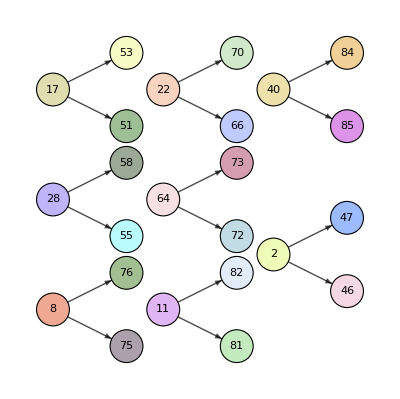

```mathematica
lineageTree[First@links]
```

```mathematica
birthDeathFrameRecord@segtrack
```

Dataset[<>]

```mathematica
(* Make apoptotic cells work *)
```

```mathematica
apoptoticCells[segtrack]
```

{}

```mathematica
(* recheck confidence Index *)
```

```mathematica
confidenceIndex[segtrack]
```

Dataset[<>]

```mathematica
(* cell as geometric region *)
```

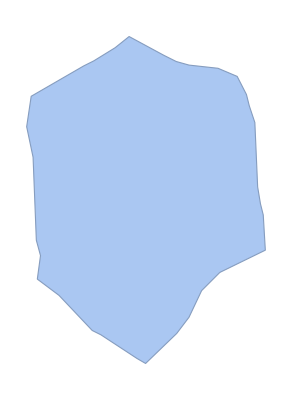
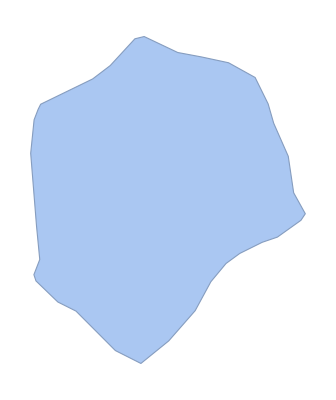
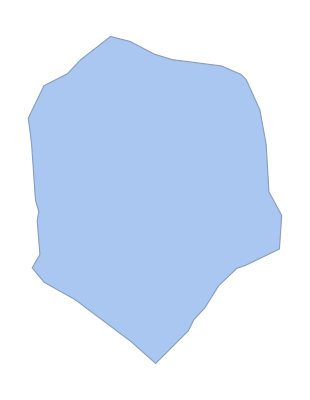
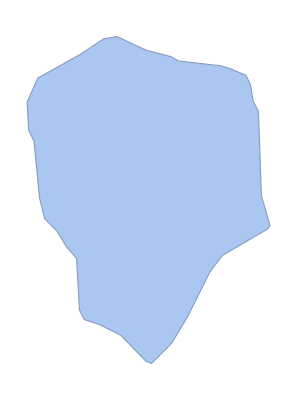
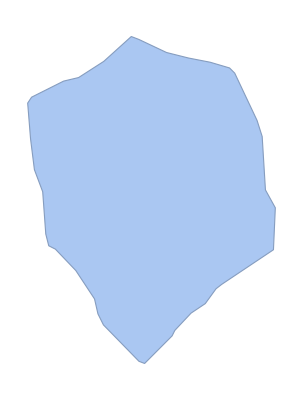
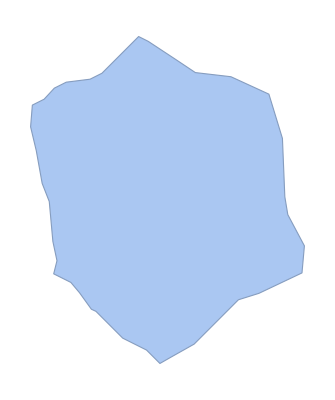

```mathematica
cellMesh[segtrack,19]
```

## Solving equation over a cell

```mathematica
Clear[x,y,cell,op];
```

```mathematica
cell=-Graphics-;
```

```mathematica
op = - Laplacian[u[x,y],{x,y}];
```

```mathematica
usol = NDSolveValue[{op==1,DirichletCondition[u[x,y]==0,True]},u,{x,y}∈cell];
```

```mathematica
ContourPlot[usol[x,y],{x,y}∈cell]
```

-Graphics-

```mathematica
Plot3D[usol[x,y],{x,y}∈cell,ColorFunction->"Rainbow",Mesh->None,PlotRange->Full,MaxRecursion->5,Axes->False]
```

-Graphics3D-

## Fusion Enabled

```mathematica
$framehistory={};
({segtrack,links}=cellTracker[lineagemappersegs,"segmented"-> True,"FusionEnabled"-> True];)//AbsoluteTiming
```

{3.14339,Null}

```mathematica
Map[Colorize]@lineagemappersegs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Colorize]@segtrack
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Max@Last@segtrack
```

103

```mathematica
lineageTable[First@links]
```

Dataset[<>]

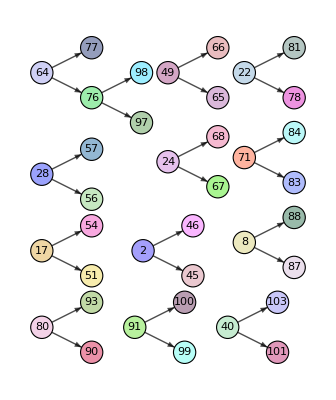

```mathematica
lineageTree[First@links]
```

```mathematica
birthDeathFrameRecord[segtrack]
```

Dataset[<>]

```mathematica
confidenceIndex[segtrack]
```

Dataset[<>]

```mathematica
(* Make apoptotic cells work *)
```

```mathematica
apoptoticCells[segtrack]
```

{}

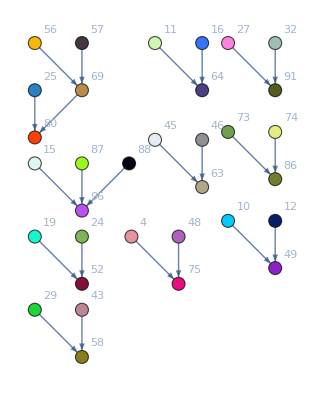

```mathematica
fusionTree[Last@links]
```

## Other tests:

```mathematica
file="C:\\Users\\aliha\\Desktop\\scripts-codes\\github codes\\lineage mapper\\ROPER MOVIES\\40X\\Ctrl1 Utr GFP\\17-12-26_Ctrl_E4-1_RSize_wat.tif";
```

```mathematica
segs=segmentImage@*Binarize/@Import@file;
```

```mathematica
$framehistory={};
({segmentedstacks,links}=cellTracker[segs,"segmented"-> True];)//AbsoluteTiming
```

{37.5516,Null}

```mathematica
ListAnimate[Map[Colorize]@segmentedstacks]
```

```mathematica
file = "C:\\Users\\aliha\\Desktop\\scripts-codes\\github codes\\lineage mapper\\ROPER MOVIES\\40X\\Ctrl2 Utr GFP\\17-12-26_Ctrl_E1-1_RSize_wat.tif";
```

```mathematica
segs=segmentImage@*Binarize/@Import@file;
```

```mathematica
$framehistory={};
({segmentedstacks,links}=cellTracker[segs,"segmented"-> True];)//AbsoluteTiming
```

{38.8421,Null}

```mathematica
ListAnimate[Map[Colorize]@segmentedstacks]
```

```mathematica
Length@segmentedstacks
```

40

```mathematica
ComponentMeasurements[segmentedstacks[[-1]],"Label"]//Length
```

172